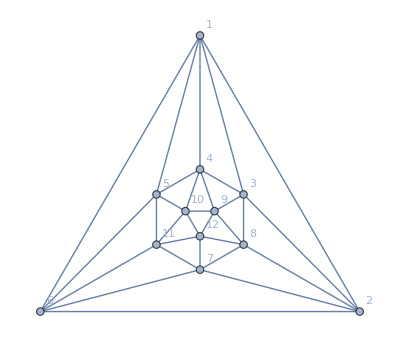

```mathematica
Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
EmbedGraph5Plantri1[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,3,4,5,6}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[1]]],1];
g=EdgeDelete[ g,{2<->3,3<->4,4<->5,5<->6,6<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
repPlantri1=Monitor[Table[
With[{k=treeKeys5[[i]]},
treeForm5[k,"colofourtree"]->ChromaticPolynomial[EmbedGraph5Plantri1[treeForm5,k],4]/24
],{i,Length[treeKeys5]}],{i,Length[treeKeys5]}]
```

{t29888→5,t3898→17,t39014→5,t3970→19,t49194→13,t49196→5,t49200→5,t49212→5,t49220→3,t56012→3,t56770→5,t58288→5,t59048→5,t7034→9,t7380→35,t7398→41,t7480→15,t7614→39,t7647→15,t7704→13,t7738→3,t778→21,t8112→21,t814→39,t820→37,t822→39,t8346→21,t840→43,t8436→7,t846→39,t8778→43,t8797→17,t8856→43,t8884→17,t9018→41,t9048→17,t9117→17,t9148→5,t922→19,t9504→45,t9522→21,t9558→43,t9564→17,t9587→17,t9720→41,t9722→19,t9753→15,t976→35,t9819→17,t982→31,t984→35,t9854→9}

```mathematica
Monitor[Table[
With[{k=Keys[withRelations5][[i]]},
ChromaticPolynomial[EmbedGraph5Plantri1[treeForm5,k],4]/24
],{i,Length[Keys[withRelations5]]}],{i,Length[Keys[withRelations5]]}]
```

```mathematica
treeForm5[29524,"graph"]
```

-Graphics-

```mathematica
Monitor[Table[
With[{k=Keys[withRelations5][[i]]},
{treeForm5[k,"colofourtree"]/.repPlantri1,k}
],{i,Length[Keys[withRelations5]]}],{i,Length[Keys[withRelations5]]}]//Sort
```

{{0,29524},{1,31984},{1,36194},{1,36898},{1,38308},{1,51478},{2,22963},{2,27337},{2,29443},{2,29497},{2,29521},{2,29527},{2,29551},{2,29560},{2,29605},{2,29608},{2,29768},{2,30262},{2,30334},{2,30496},{2,31711},{2,31714},{2,31738},{2,31954},{2,36085},{2,36086},{2,36112},{2,36166},{2,49208},{2,49210},{2,49216},{3,7738},{3,11950},{3,20812},{3,22318},{3,23770},{3,25168},{3,30586},{3,31444},{3,31492},{3,31924},{3,32684},{3,33916},{3,35434},{3,35978},{3,36030},{3,36138},{3,46942},{3,49220},{3,49972},{3,56012},{4,448},{4,9841},{4,9844},{4,11680},{4,20776},{4,22960},{4,22990},{4,23044},{4,24922},{4,27256},{4,27340},{4,27364},{4,28795},{4,28876},{4,29281},{4,29416},{4,29446},{4,29494},{4,29515},{4,29523},{4,29525},{4,29533},{4,29542},{4,29602},{4,29633},{4,29767},{4,29797},{4,30253},{4,31468},{4,31684},{4,31708},{4,33834},{4,35406},{4,36004},{4,36058},{4,36084},{4,36817},{4,38281},{4,49207},{4,51475},{5,3524},{5,9148},{5,10552},{5,16160},{5,23072},{5,26852},{5,27610},{5,28308},{5,29888},{5,29938},{5,30082},{5,30406},{5,31224},{5,36736},{5,38254},{5,39014},{5,42404},{5,48460},{5,49196},{5,49200},{5,49212},{5,51472},{5,52232},{5,56770},{5,58288},{5,59048},{6,400},{6,3280},{6,4920},{6,7654},{6,7657},{6,7735},{6,9760},{6,9763},{6,9814},{6,9842},{6,9850},{6,11947},{6,13340},{6,14748},{6,16052},{6,17568},{6,20803},{6,22234},{6,22237},{6,22315},{6,22720},{6,22882},{6,22936},{6,22954},{6,22964},{6,22981},{6,23041},{6,23518},{6,25141},{6,26608},{6,27259},{6,27310},{6,27328},{6,27334},{6,27336},{6,27355},{6,27580},{6,28768},{6,28792},{6,28804},{6,28873},{6,29038},{6,29200},{6,29254},{6,29257},{6,29278},{6,29282},{6,29305},{6,29434},{6,29440},{6,29442},{6,29469},{6,29496},{6,29506},{6,29512},{6,29520},{6,29537},{6,29577},{6,29766},{6,29857},{6,30010},{6,30172},{6,30244},{6,31194},{6,31441},{6,31465},{6,31681},{6,32441},{6,33889},{6,35353},{6,35977},{6,36003},{6,36057},{6,43908},{6,46932},{6,49198},{6,49204},{6,49206},{6,49963},{6,56011},{7,4222},{7,5620},{7,8436},{7,11244},{7,14044},{7,15454},{7,21510},{7,24414},{7,29232},{7,29328},{7,29648},{7,33158},{7,40144},{7,41650},{7,46184},{8,608},{8,1093},{8,1174},{8,1872},{8,2124},{8,2554},{8,3281},{8,4650},{8,4674},{8,5590},{8,6320},{8,7006},{8,7458},{8,9112},{8,9121},{8,9139},{8,9574},{8,9598},{8,9599},{8,9733},{8,9823},{8,9838},{8,10228},{8,10998},{8,11704},{8,11920},{8,13258},{8,13312},{8,14016},{8,15372},{8,16159},{8,20047},{8,20050},{8,20484},{8,20695},{8,20773},{8,20785},{8,22038},{8,22717},{8,22721},{8,22744},{8,22933},{8,22951},{8,22962},{8,23689},{8,24144},{8,24898},{8,25138},{8,26851},{8,27094},{8,27229},{8,27247},{8,27255},{8,27282},{8,27579},{8,28218},{8,28714},{8,28765},{8,28777},{8,28794},{8,28848},{8,29037},{8,29173},{8,29176},{8,29272},{8,29296},{8,29353},{8,29413},{8,29417},{8,29460},{8,29488},{8,29493},{8,29514},{8,29517},{8,29574},{8,29737},{8,29929},{8,30001},{8,30163},{8,30981},{8,33050},{8,33808},{8,33888},{8,35326},{8,35352},{8,39382},{8,39392},{8,40896},{8,42392},{8,46939},{8,48456},{8,49195},{8,49197},{8,49203},{8,52976},{9,2824},{9,7034},{9,7576},{9,7732},{9,9854},{9,11944},{9,16864},{9,18274},{9,20794},{9,22156},{9,22312},{9,22908},{9,23016},{9,25114},{9,27070},{9,27118},{9,29128},{9,29378},{9,29706},{9,31438},{9,32198},{9,33862},{9,34620},{9,35272},{9,35976},{9,37548},{9,44662},{9,49954},{9,50718},{9,56010},{10,367},{10,445},{10,473},{10,637},{10,728},{10,1102},{10,1800},{10,2034},{10,2551},{10,2578},{10,3199},{10,3253},{10,3277},{10,3404},{10,3523},{10,4132},{10,4890},{10,5377},{10,6925},{10,6952},{10,7627},{10,7707},{10,8184},{10,8820},{10,9493},{10,9517},{10,9571},{10,9734},{10,9811},{10,9832},{10,9840},{10,10543},{10,11677},{10,13232},{10,16078},{10,16132},{10,16783},{10,18247},{10,18980},{10,20056},{10,20533},{10,20749},{10,20775},{10,21186},{10,21967},{10,22207},{10,22639},{10,22693},{10,22711},{10,22735},{10,22792},{10,22817},{10,22855},{10,22873},{10,22879},{10,22959},{10,23446},{10,23680},{10,24895},{10,26527},{10,26581},{10,26605},{10,26609},{10,26732},{10,27013},{10,27253},{10,27273},{10,27307},{10,27309},{10,27325},{10,27327},{10,27330},{10,27333},{10,27519},{10,28065},{10,28552},{10,28687},{10,28767},{10,28786},{10,28791},{10,28845},{10,29008},{10,29174},{10,29197},{10,29209},{10,29223},{10,29269},{10,29280},{10,29350},{10,29407},{10,29431},{10,29433},{10,29436},{10,29439},{10,29485},{10,29513},{10,29529},{10,29677},{10,29736},{10,30954},{10,30978},{10,33157},{10,33807},{10,34539},{10,35325},{10,37521},{10,39380},{10,39388},{10,40140},{10,41640},{10,42403},{10,44659},{10,45416},{10,46172},{10,46930},{10,46938},{10,48451},{10,50715},{10,54492},{10,57528},{11,1171},{11,1426},{11,2473},{11,7003},{11,7387},{11,11701},{11,11917},{11,12650},{11,19969},{11,20060},{11,20557},{11,20721},{11,20758},{11,22287},{11,22856},{11,22899},{11,23013},{11,23608},{11,24871},{11,25111},{11,25868},{11,26989},{11,27109},{11,27550},{11,29186},{11,29826},{11,33781},{11,33861},{11,35245},{11,35271},{11,43156},{11,46936},{11,47694},{11,53734},{11,55252},{12,364},{12,373},{12,391},{12,1336},{12,2794},{12,3271},{12,6926},{12,7411},{12,7483},{12,7573},{12,7645},{12,7651},{12,7653},{12,8893},{12,9031},{12,9057},{12,9109},{12,9490},{12,9491},{12,9526},{12,9595},{12,9751},{12,9757},{12,9759},{12,9813},{12,10300},{12,10462},{12,11217},{12,13963},{12,15427},{12,16051},{12,20048},{12,20767},{12,21991},{12,22153},{12,22225},{12,22227},{12,22231},{12,22233},{12,22708},{12,22789},{12,22881},{12,22927},{12,22935},{12,22952},{12,22953},{12,23437},{12,24411},{12,26599},{12,27067},{12,27085},{12,27091},{12,27246},{12,27249},{12,27301},{12,27490},{12,27984},{12,28056},{12,28525},{12,28549},{12,28711},{12,28713},{12,28764},{12,28783},{12,28800},{12,29007},{12,29182},{12,29199},{12,29245},{12,29247},{12,29251},{12,29253},{12,29270},{12,29277},{12,29325},{12,29415},{12,29487},{12,29502},{12,29676},{12,30951},{12,42394},{12,42400},{12,46929},{12,48448},{12,48450},{13,1075},{13,1146},{13,3038},{13,3173},{13,5350},{13,5374},{13,7704},{13,9094},{13,9130},{13,9834},{13,16158},{13,19780},{13,20029},{13,21886},{13,22613},{13,22662},{13,23365},{13,23599},{13,26821},{13,26850},{13,27036},{13,27549},{13,28624},{13,29920},{13,30738},{13,33076},{13,33130},{13,46927},{13,46935},{13,49194},{14,168},{14,286},{14,365},{14,377},{14,442},{14,607},{14,697},{14,1066},{14,1090},{14,2733},{14,3172},{14,3250},{14,3279},{14,3493},{14,3979},{14,4380},{14,4428},{14,6779},{14,7306},{14,8869},{14,9111},{14,9499},{14,9503},{14,9589},{14,9730},{14,9805},{14,9829},{14,9837},{14,10219},{14,11674},{14,12407},{14,13176},{14,13284},{14,14667},{14,17541},{14,19966},{14,20020},{14,20452},{14,20461},{14,20530},{14,20548},{14,20668},{14,20692},{14,20694},{14,20712},{14,20746},{14,20772},{14,20781},{14,21501},{14,22284},{14,22612},{14,22636},{14,22709},{14,22719},{14,22852},{14,22870},{14,22924},{14,22932},{14,24868},{14,25625},{14,26365},{14,26500},{14,26501},{14,26578},{14,26986},{14,27093},{14,27220},{14,27226},{14,27244},{14,27252},{14,27306},{14,27489},{14,27975},{14,28471},{14,28684},{14,28705},{14,28759},{14,28773},{14,28785},{14,29097},{14,29271},{14,29404},{14,29405},{14,29647},{14,33780},{14,35244},{14,40135},{14,42391},{14,43147},{14,43905},{14,46183},{14,47685},{14,48447},{14,53733},{14,55251},{15,2496},{15,2569},{15,3522},{15,6706},{15,6943},{15,7480},{15,7647},{15,9753},{15,9830},{15,9846},{15,10534},{15,11214},{15,13936},{15,15346},{15,16077},{15,16131},{15,22063},{15,22146},{15,22764},{15,24384},{15,26366},{15,27060},{15,27822},{15,28480},{15,28621},{15,28948},{15,30711},{15,30735},{15,42402},{15,48442},{16,72},{16,1012},{16,1092},{16,1143},{16,1395},{16,1620},{16,2470},{16,3037},{16,3190},{16,3196},{16,3268},{16,3433},{16,4647},{16,4860},{16,5347},{16,6077},{16,6922},{16,7384},{16,7455},{16,7546},{16,7624},{16,7626},{16,8355},{16,8811},{16,9085},{16,9103},{16,9514},{16,9597},{16,9724},{16,9810},{16,9831},{16,13124},{16,13231},{16,19699},{16,19709},{16,19804},{16,20044},{16,20475},{16,20506},{16,20686},{16,20748},{16,20764},{16,21957},{16,21964},{16,22126},{16,22204},{16,22206},{16,22684},{16,22690},{16,22716},{16,22846},{16,22872},{16,22878},{16,26518},{16,26524},{16,26596},{16,26597},{16,26607},{16,27010},{16,27012},{16,27082},{16,27228},{16,27298},{16,27300},{16,28444},{16,28543},{16,28551},{16,28710},{16,28756},{16,29170},{16,29191},{16,29196},{16,29205},{16,29412},{16,29511},{16,33049},{16,39372},{16,40887},{16,41647},{16,52975},{17,1306},{17,1335},{17,2284},{17,2544},{17,2793},{17,3269},{17,3898},{17,5134},{17,6683},{17,6754},{17,6978},{17,8797},{17,8884},{17,9048},{17,9117},{17,9564},{17,9587},{17,9819},{17,10291},{17,10453},{17,10974},{17,13962},{17,15426},{17,19805},{17,19940},{17,20434},{17,20754},{17,21420},{17,22844},{17,24168},{17,26761},{17,27460},{17,27741},{17,27813},{17,28453},{17,28596},{17,28947},{17,29214},{17,33156},{17,40132},{17,42393},{17,42399},{17,46180},{17,48439},{17,48441},{18,346},{18,382},{18,488},{18,1084},{18,1476},{18,1944},{18,2542},{18,2548},{18,2550},{18,2930},{18,3198},{18,3244},{18,3252},{18,3276},{18,6682},{18,6844},{18,6916},{18,7330},{18,7402},{18,7408},{18,7564},{18,7566},{18,7572},{18,7618},{18,7642},{18,7644},{18,7650},{18,8788},{18,8866},{18,9028},{18,9030},{18,9108},{18,9516},{18,9562},{18,9568},{18,9570},{18,9586},{18,9732},{18,9748},{18,9750},{18,9756},{18,9802},{18,16050},{18,20038},{18,20524},{18,20532},{18,20766},{18,21910},{18,21982},{18,21988},{18,22060},{18,22144},{18,22152},{18,22198},{18,22222},{18,22224},{18,22230},{18,22638},{18,22692},{18,22710},{18,22926},{18,23356},{18,26284},{18,26338},{18,26362},{18,26572},{18,26820},{18,27058},{18,27066},{18,27084},{18,27090},{18,28468},{18,28522},{18,28524},{18,28540},{18,28548},{18,28678},{18,28686},{18,28702},{18,28704},{18,28758},{18,29172},{18,29242},{18,29244},{18,29250},{18,29406},{18,30708},{18,39368},{18,39384},{18,46926},{19,922},{19,1098},{19,2332},{19,3492},{19,3970},{19,6870},{19,9722},{19,11190},{19,13882},{19,15400},{19,19732},{19,20040},{19,21258},{19,24408},{19,26258},{19,28918},{19,29166},{19,29322},{19,40134},{19,46174},{20,97},{20,218},{20,417},{20,546},{20,850},{20,1063},{20,1791},{20,2203},{20,2463},{20,2487},{20,2524},{20,2956},{20,3010},{20,3034},{20,3169},{20,3270},{20,3403},{20,5107},{20,5131},{20,6697},{20,6751},{20,6898},{20,6975},{20,7377},{20,7410},{20,9004},{20,9022},{20,9082},{20,9100},{20,9594},{20,9804},{20,10971},{20,13935},{20,14586},{20,15345},{20,17514},{20,19939},{20,20046},{20,20425},{20,20449},{20,20457},{20,20665},{20,20691},{20,20745},{20,21990},{20,22035},{20,22630},{20,22653},{20,22843},{20,22950},{20,24141},{20,26356},{20,26489},{20,26497},{20,26526},{20,26580},{20,26604},{20,27004},{20,27027},{20,27217},{20,27324},{20,28470},{20,28516},{20,29164},{20,29188},{20,29430},{20,29484},{20,33075},{20,33129},{20,39379},{20,43902},{21,778},{21,2704},{21,2764},{21,3432},{21,3736},{21,6818},{21,6914},{21,7570},{21,8112},{21,8346},{21,9522},{21,20052},{21,20740},{21,21492},{21,22150},{21,22854},{21,26354},{21,27064},{21,28476},{21,29162},{21,29646},{21,40126},{21,41638},{21,41646},{21,46182},{22,122},{22,145},{22,283},{22,309},{22,361},{22,606},{22,919},{22,985},{22,1065},{22,1071},{22,1089},{22,1305},{22,2308},{22,3026},{22,3028},{22,3161},{22,3163},{22,3187},{22,3241},{22,3249},{22,3889},{22,6924},{22,7303},{22,7623},{22,8770},{22,8842},{22,8860},{22,8868},{22,9084},{22,9090},{22,9102},{22,9487},{22,9508},{22,9588},{22,9721},{22,10210},{22,11187},{22,13855},{22,15319},{22,19697},{22,19705},{22,19723},{22,19777},{22,19959},{22,20017},{22,20451},{22,20521},{22,20529},{22,20683},{22,20685},{22,21177},{22,21883},{22,22203},{22,22609},{22,22635},{22,22681},{22,22761},{22,24381},{22,26257},{22,26491},{22,26515},{22,26569},{22,26598},{22,26731},{22,26760},{22,26979},{22,27009},{22,27219},{22,27225},{22,27732},{22,28542},{22,28675},{22,28683},{22,28782},{22,29190},{22,29268},{22,40131},{22,42390},{22,46171},{22,48438},{23,1246},{23,8274},{23,20036},{23,29178},{23,41644},{24,16},{24,26},{24,193},{24,257},{24,337},{24,355},{24,357},{24,414},{24,577},{24,666},{24,751},{24,894},{24,1011},{24,1081},{24,2250},{24,2323},{24,2461},{24,2469},{24,2929},{24,3189},{24,3195},{24,3655},{24,4620},{24,4644},{24,5104},{24,5834},{24,6624},{24,6679},{24,6861},{24,6913},{24,7375},{24,7383},{24,7399},{24,7452},{24,7537},{24,7563},{24,7615},{24,7617},{24,8785},{24,9027},{24,9483},{24,9489},{24,9513},{24,9729},{24,10947},{24,13150},{24,13204},{24,13881},{24,15399},{24,19770},{24,19801},{24,19957},{24,20025},{24,20466},{24,20505},{24,21411},{24,21876},{24,21955},{24,21963},{24,21979},{24,22117},{24,22143},{24,22195},{24,22197},{24,22601},{24,22627},{24,22683},{24,22689},{24,24165},{24,26281},{24,26353},{24,26577},{24,26985},{24,27057},{24,27243},{24,27459},{24,28441},{24,28467},{24,28521},{24,28593},{24,33048},{24,40123},{24,40878},{24,46179},{24,52974},{25,1009},{25,7543},{25,19963},{25,20503},{25,20659},{25,20667},{25,20737},{25,22123},{25,22851},{25,26983},{26,49},{26,121},{26,363},{26,369},{26,823},{26,847},{26,1003},{26,1083},{26,2274},{26,2443},{26,2539},{26,2541},{26,2547},{26,2703},{26,2763},{26,2953},{26,3025},{26,3243},{26,3727},{26,4404},{26,6575},{26,6601},{26,6671},{26,6673},{26,6726},{26,6835},{26,6895},{26,7329},{26,7401},{26,7407},{26,7545},{26,8103},{26,8761},{26,8787},{26,8793},{26,8802},{26,8857},{26,8865},{26,9001},{26,9019},{26,9021},{26,9081},{26,9479},{26,9481},{26,9559},{26,9561},{26,9567},{26,9723},{26,13230},{26,19795},{26,19965},{26,20019},{26,20035},{26,20523},{26,21249},{26,21909},{26,21961},{26,21981},{26,21987},{26,22603},{26,22707},{26,22869},{26,22923},{26,26329},{26,26517},{26,26523},{26,26977},{26,27001},{26,27003},{26,27297},{26,28443},{26,28513},{26,28515},{26,28677},{26,28755},{26,28917},{26,29169},{26,40125},{26,41637},{26,46173},{27,1057},{27,2467},{27,3171},{27,6841},{27,7327},{27,7381},{27,7561},{27,7569},{27,20011},{27,20497},{27,20739},{27,21907},{27,22125},{27,22141},{27,22149},{27,22611},{27,22845},{27,26335},{27,27055},{27,27063},{28,136},{28,190},{28,276},{28,300},{28,353},{28,517},{28,769},{28,1062},{28,1216},{28,1245},{28,1710},{28,2227},{28,2521},{28,2523},{28,3001},{28,3007},{28,3160},{28,6655},{28,6817},{28,6921},{28,7296},{28,8031},{28,8265},{28,9495},{28,9505},{28,10944},{28,13854},{28,15318},{28,19696},{28,19793},{28,19928},{28,20043},{28,20430},{28,20443},{28,20448},{28,20763},{28,22032},{28,22629},{28,24138},{28,26488},{28,26499},{28,26571},{28,27081},{28,28449},{28,28701},{28,29161},{28,29403},{28,39376},{28,41635},{28,41643},{29,3036},{29,9076},{29,9828},{29,26364},{29,28462},{30,774},{30,841},{30,1548},{30,1782},{30,2299},{30,2305},{30,2674},{30,3402},{30,6806},{30,6843},{30,6915},{30,7321},{30,8839},{30,8841},{30,8859},{30,9003},{30,9507},{30,19728},{30,20037},{30,22221},{30,26246},{30,28539},{30,29163},{30,29241},{30,39370},{30,39378},{31,982},{31,19936},{31,20422},{31,20656},{31,20664},{32,14},{32,22},{32,63},{32,342},{32,576},{32,891},{32,2281},{32,2460},{32,2918},{32,2947},{32,3646},{32,4617},{32,6670},{32,6897},{32,7374},{32,8784},{32,13123},{32,19689},{32,21168},{32,21954},{32,26595},{32,26730},{32,29187},{32,40122},{32,46170},{33,849},{33,1008},{33,1054},{33,2515},{33,2955},{33,3009},{33,3033},{33,3168},{33,3267},{33,6889},{33,7534},{33,7641},{33,8995},{33,9073},{33,9747},{33,9801},{33,19720},{33,19803},{33,19930},{33,20424},{33,20502},{33,21901},{33,22114},{33,26254},{33,26275},{33,26283},{33,26337},{33,26361},{33,28435},{33,28459},{34,87},{34,165},{34,256},{34,274},{34,334},{34,352},{34,742},{34,1002},{34,2193},{34,2241},{34,2926},{34,4377},{34,4401},{34,6615},{34,6723},{34,7302},{34,7536},{34,9486},{34,13149},{34,13203},{34,19792},{34,20016},{34,20440},{34,20682},{34,21952},{34,21960},{34,22600},{34,26496},{34,27216},{34,28440},{35,976},{35,984},{35,1000},{35,1056},{35,2307},{35,2458},{35,2466},{35,3027},{35,3162},{35,6598},{35,6681},{35,6832},{35,7326},{35,7372},{35,7380},{35,7542},{35,8779},{35,8833},{35,9075},{35,9099},{35,9585},{35,19768},{35,19774},{35,19954},{35,20008},{35,20496},{35,21880},{35,21882},{35,21906},{35,22116},{35,22608},{35,26326},{35,26355},{35,26982},{35,28461},{36,40},{36,110},{36,118},{36,280},{36,282},{36,360},{36,516},{36,838},{36,2520},{36,2998},{36,6574},{36,7294},{36,7300},{36,8022},{36,8758},{36,8766},{36,9000},{36,9478},{36,19956},{36,20442},{36,20494},{36,20520},{36,20658},{36,22122},{36,22194},{36,22680},{36,26490},{36,26976},{36,28674},{36,41634},{37,766},{37,820},{37,2440},{37,6814},{37,19938},{37,19962},{37,20416},{37,20736},{37,22842},{37,26974},{38,94},{38,112},{38,245},{38,336},{38,354},{38,487},{38,747},{38,1215},{38,1467},{38,1701},{38,2200},{38,2296},{38,2920},{38,2944},{38,6834},{38,6894},{38,7320},{38,8760},{38,8838},{38,9480},{38,19685},{38,19701},{38,21978},{38,22626},{38,26514},{38,26568},{38,27000},{38,28512},{38,39367},{38,39375},{39,814},{39,822},{39,846},{39,2224},{39,2434},{39,2442},{39,2952},{39,3186},{39,3240},{39,6652},{39,6840},{39,6886},{39,7318},{39,7614},{39,8992},{39,19722},{39,19776},{39,20010},{39,21874},{39,22140},{39,22602},{39,26248},{39,26272},{39,26280},{39,27054},{40,45},{40,1539},{40,2673},{40,6563},{40,39369},{41,768},{41,1080},{41,2226},{41,2512},{41,2514},{41,3000},{41,3006},{41,6646},{41,6678},{41,6808},{41,7398},{41,8776},{41,9018},{41,9720},{41,19714},{41,19800},{41,21900},{41,26256},{41,26328},{41,28432},{42,328},{42,2928},{42,7560},{42,21898},{42,26334},{43,840},{43,2298},{43,2304},{43,2538},{43,6592},{43,6600},{43,6672},{43,8778},{43,8830},{43,8832},{43,8856},{43,8994},{43,9558},{43,19794},{43,28434},{44,973},{44,981},{44,19693},{44,19927},{44,20421},{45,2218},{45,2272},{45,2280},{45,2946},{45,6654},{45,6888},{45,6912},{45,9504},{45,26352},{45,28458},{48,6},{48,13},{48,54},{48,109},{48,120},{48,162},{48,253},{48,271},{48,273},{48,333},{48,739},{48,975},{48,2917},{48,3024},{48,4374},{48,7293},{48,7299},{48,8752},{48,8757},{48,9072},{48,13122},{48,19765},{48,19935},{48,20413},{48,20439},{48,20655},{48,21879},{48,21951},{48,26274},{48,26487},{49,760},{49,2278},{49,6816},{49,20034},{49,29160},{50,37},{50,279},{50,765},{50,811},{50,819},{50,1053},{50,2431},{50,2439},{50,3159},{50,6571},{50,6805},{50,7291},{50,19687},{50,19695},{50,19719},{50,19929},{50,20415},{50,20493},{50,22113},{50,26245},{52,247},{52,325},{52,741},{52,813},{52,999},{52,2223},{52,2433},{52,2457},{52,2925},{52,6589},{52,6597},{52,6643},{52,7371},{52,7533},{52,19711},{52,19767},{52,19773},{52,21871},{52,21873},{52,26253},{56,2},{56,18},{56,85},{56,327},{56,486},{56,1458},{56,2199},{56,2215},{56,2919},{56,6651},{56,6831},{56,7317},{56,21897},{56,26325},{56,39366},{58,39},{58,91},{58,117},{58,255},{58,733},{58,757},{58,837},{58,2197},{58,2217},{58,2271},{58,2511},{58,2997},{58,6565},{58,6645},{58,6669},{58,6813},{58,8749},{58,8775},{58,8991},{58,19713},{58,19953},{58,20007},{58,22599},{58,26247},{58,26973},{60,93},{60,111},{60,2191},{60,2295},{60,2943},{60,6591},{60,6885},{60,8751},{60,8829},{60,26271},{62,31},{62,351},{62,759},{62,2269},{62,2277},{62,6573},{62,6807},{62,9477},{62,19791},{62,28431},{66,244},{66,738},{66,972},{66,19684},{66,19692},{72,10},{72,36},{72,252},{72,730},{72,810},{72,2430},{72,6562},{72,19686},{72,19926},{72,20412},{76,28},{76,82},{76,246},{76,270},{76,732},{76,2196},{76,6570},{76,7290},{76,19764},{76,21870},{78,84},{78,2190},{78,2214},{78,6588},{78,6642},{80,4},{80,12},{80,90},{80,324},{80,756},{80,2188},{80,2916},{80,6804},{80,19710},{80,26244},{84,30},{84,108},{84,2268},{84,6564},{84,8748},{104,1},{104,9},{104,243},{104,729},{104,19683},{112,3},{112,27},{112,81},{112,2187},{112,6561},{160,0}}

```mathematica
e
```

```mathematica
treeForm5["full","vertexsets"]={{1},{2},{3},{4},{5},{6}}
```

{{1},{2},{3},{4},{5},{6}}

```mathematica
Keys[treeForm5["full"]]
```

{signature,colofour,colortable,comp,compwhy,matrix,graph,vertexsets,vertices,relations,colofourtree,colortabletree}

```mathematica
treeForm5["full","colofourtree"]/.repPlantri1
```

10

```mathematica
Graph[EmbedGraph5Plantri1[treeForm5,"full"],VertexLabels->"Name"]//ChromaticPolynomial[#,4]&
```

240

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri1[treeForm5,"full"],4]/24
```

Part::partw: Part 6 of {{1}, {2}, {3}, {4}, {5}} does not exist.

Part::pkspec1: The expression {{1}, {2}, {3}, {4}, {5}} cannot be used as a part specification.

Part::partw: Part 6 of {{1}, {2}, {3}, {4}, {5}} does not exist.

Part::pkspec1: The expression {{1}, {2}, {3}, {4}, {5}} cannot be used as a part specification.

Part::partw: Part 6 of {{1}, {2}, {3}, {4}, {5}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pkspec1: The expression {{1}, {2}, {3}, {4}, {5}} cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

10

```mathematica
Reduce[Fold[And,Table[treeForm5[k,"colofour"]/.{v14x23x5->0,v13x2x45->0,v15x24x3->0,v12x35x4->0,v1x25x34->0}//Simplify,{k,treeKeys5}]], baseGraphAxioma5Vars]
```

Reduce::naqs: « 1 » is not a quantified system of equations and inequalities.

Reduce[v1x2345&&v125x3x4+v135x24+v135x2x4+v15x2x3x4&&v1345x2&&v125x34+v125x3x4+v135x2x4+v15x2x34+v15x2x3x4&&v12x345+v12x34x5+v12x3x45+v12x3x4x5&&v12x345+v12x3x45&&v12x345&&v12x345+v12x34x5&&v12x345&&v123x45&&v1235x4&&v1234x5&&v12345&&v1245x3+v1x245x3&&v12x3x45+v12x3x4x5+v14x235+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v124x35+v124x3x5+v1x234x5+v1x24x35+v1x24x3x5&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v12x345+v14x2x35+v1x2x345+v1x2x35x4&&v124x35+v124x3x5+v1x245x3+v1x24x35+v1x24x3x5&&v124x35+v1x24x35&&v1234x5+v12x34x5+v134x2x5+v1x234x5+v1x2x34x5&&v125x3x4+v145x23+v145x2x3+v15x23x4+v15x2x3x4&&v123x4x5+v12x34x5+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x23x4x5+v1x25x3x4+v1x2x34x5+v1x2x3x4x5&&v123x4x5+v12x3x4x5+v13x25x4+v13x2x4x5+v14x235+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5&&v123x45+v123x4x5+v12x3x45+v12x3x4x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5&&v125x34+v125x3x4+v145x2x3+v15x2x34+v15x2x3x4&&v123x45+v123x4x5+v12x34x5+v12x3x45+v12x3x4x5+v134x2x5+v13x2x4x5+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5&&v1245x3&&v123x45+v123x4x5+v12x3x45+v12x3x4x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v12x34x5+v12x3x45+v12x3x4x5+v15x234+v15x23x4+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5&&v12x34x5+v15x234+v15x2x34+v1x234x5+v1x2x34x5&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v125x34+v125x3x4+v1x235x4+v1x25x3x4&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v125x34+v125x3x4+v1x245x3+v1x25x3x4&&v12x345+v12x34x5+v15x2x34+v1x2x345+v1x2x34x5&&v125x34&&v1234x5+v124x3x5+v13x24x5+v1x234x5+v1x24x3x5&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v12x345+v12x34x5+v1x234x5+v1x2x345+v1x2x34x5&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v12x345+v1x235x4+v1x2x345+v1x2x35x4&&v12x345+v12x3x45+v1x23x45+v1x2x345+v1x2x3x45&&v12x345+v12x34x5+v12x3x45+v12x3x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&v12x345+v12x3x45+v1x245x3+v1x2x345+v1x2x3x45&&v12x345+v1x24x35+v1x2x345+v1x2x35x4&&v124x3x5+v12x34x5+v12x3x4x5+v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x34x5+v1x2x3x4x5&&v12x345+v12x34x5+v1x2x345+v1x2x34x5&&v124x35+v124x3x5+v12x3x4x5+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5&&v124x3x5+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5&&v12x345+v1x2x345,{v12345,v1234x5,v1235x4,v123x45,v123x4x5,v1245x3,v124x35,v124x3x5,v125x34,v125x3x4,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1345x2,v134x25,v134x2x5,v135x24,v135x2x4,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v145x23,v145x2x3,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v1x2x3x4x5}]